```mathematica
mgmomentx=Flatten[Import["mmtx_pllndata.dat"]];
mgmomenty=Flatten[Import["mmty_pllndata.dat"]];
Max[mgmomentx];
Min[mgmomentx];
Max[mgmomenty];
Min[mgmomenty];
```

```mathematica
plmgmomentx=Table[{n,mgmomentx[[n]]},{n,1,Length[mgmomentx]}];
plmgmomenty=Table[{n,mgmomenty[[n]]},{n,1,Length[mgmomenty]}];
```

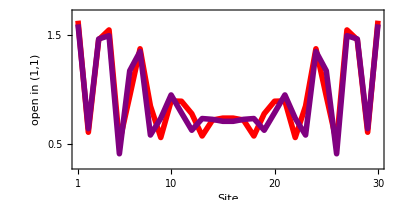

```mathematica
lineplot=ListPlot[{plmgmomentx,plmgmomenty},Joined->True,Frame->True,PlotRange->{{1,30},{0.3,1.7}},FrameTicks->{{{{-0.5,-0.5,0.018},{0,0,0.018},{0.5,0.5,0.018},{1,1,0.018},{1.5,1.5,0.018},{2,2,0.018}},{{-0.5,Null,0.018},{0,Null,0.018},{0.5,Null,0.018},{1,Null,0.018},{1.5,Null,0.018},{2,Null,0.018}}},{{{1,1,0.018},{10,10,0.018},{20,20,0.018},{30,30,0.018}},
{{1,Null,0.018},{10,Null,0.018},{20,Null,0.018},{30,Null,0.018}}}},GridLines->{None,{0}},
GridLinesStyle->Directive[Thickness[0.005],Black,50],
AspectRatio->0.5,FrameStyle->Directive[Thickness[0.006],Black,25],LabelStyle->{FontFamily->"TimesNewRoman",Black,FontSize->50},
FrameLabel->{{Style["open in (1,1)",30,Red,FontFamily->"TimesNewRoman"],Style["open in (OverBar[1]1)",30,Purple,FontFamily->"TimesNewRoman"]},
{Style["Site",30,FontFamily->"TimesNewRoman"],""}},ImagePadding->{{72,45},{70,17}},
PlotStyle->{{Red,Thickness[0.01]},{Purple,Thickness[0.01]}}]
Export["line_density_and_moment.eps",lineplot];
```